{42}

{84.}

Average Number of particles for energy levels 0-17:

{2.,2.,2.,2.,2.,2.,1.90476,1.80952,1.47619,1.19048,0.809524,0.52381,0.190476,0.0952381,0.,0.,0.}

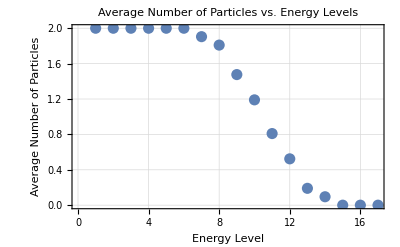

```mathematica
pj = ({{4, 4, 1, 4, 16, 4, 4, 4, 1}});
n = ({{2, 2, 2, 2, 2, 2, 2, 2, 2, 1, 0, 0, 0, 1, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 2, 2, 0, 1, 0, 1, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 2, 2, 0, 0, 2, 0, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 2, 1, 2, 0, 0, 1, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 2, 1, 1, 1, 1, 0, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 1, 2, 2, 0, 1, 0, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 1, 2, 2, 2, 1, 0, 0, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 1, 2, 1, 2, 0, 0, 0, 0, 0, 0}, {2, 2, 2, 2, 2, 2, 2, 2, 0, 2, 2, 0, 0, 0, 0, 0, 0}});
nParticles = 20;
Ω = Accumulate[Transpose[pj]][[-1]]
N[pj . Transpose[Transpose[n][[1]]]]
probs = ConstantArray[0, Length[Transpose[n]]];
For[i = 1, i <= Length[Transpose[n]], i++, 
	probs[[i]] = N[1/(nParticles Ω)pj . Transpose[Transpose[n][[i]]]][[1]];
];
Print["Average Number of particles for energy levels 0-15:"]
nParticles * probs
ListPlot[Transpose[{Range[Length[probs]], nParticles * probs}], PlotStyle -> PointSize[0.02], Frame -> True, 
   FrameLabel -> {"Energy Level", "Average Number of Particles"}, GridLines -> Automatic, 
   GridLinesStyle -> LightGray, PlotLabel -> "Average Number of Particles vs. Energy Levels"]
```